```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis/MVT_dudl_allvol_alltemp"];
dudlfiles={"dUdL_1__4685.1_300","dUdL_1__4685.2_760","dUdL_1__4685.3_1900", "dUdL_1__4685.4_2500","dUdL_1__4685.5_3200","dUdL_1__4685.6_3805","dUdL_2__4730.1_300","dUdL_2__4730.2_760","dUdL_2__4730.3_1900","dUdL_2__4730.4_2500","dUdL_2__4730.5_3200","dUdL_2__4730.6_3805","dUdL_3__4759.1_300","dUdL_3__4759.2_760","dUdL_3__4759.3_1900","dUdL_3__4759.4_2500","dUdL_3__4759.5_3200","dUdL_3__4759.6_3805","dUdL_4__4801.1_300","dUdL_4__4801.2_760","dUdL_4__4801.3_1900","dUdL_4__4801.4_2500","dUdL_4__4801.5_3200","dUdL_4__4801.6_3805","dUdL_5__4850.1_300","dUdL_5__4850.2_760","dUdL_5__4850.3_1900","dUdL_5__4850.4_2500","dUdL_5__4850.5_3200","dUdL_5__4850.6_3805"};
dudldatafull=Table[ReadList[dudlfiles[[i]],{Number, Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,30}];
dudldata=Table[dudldatafull[[j]][[501;;15000]],{j,1,30}]
(*step time(fs) temp(K) average U(meV/at) Uref dUdL average offset*)
```

{{{501,501.,325.,300.3,36.17,39.88,-3.71,-4.03,-4.13},{502,502.,332.3,300.4,35.88,39.54,-3.66,-4.03,-4.13},{503,503.,340.3,300.5,35.62,39.21,-3.59,-4.03,-4.12},{504,504.,343.7,300.6,35.44,38.96,-3.52,-4.03,-4.12},14493,{14998,14998.,331.1,300.7,40.28,43.67,-3.39,-3.81,-3.81},{14999,14999.,338.7,300.7,39.96,43.47,-3.51,-3.81,-3.81},{15000,15000.,345.6,300.7,39.64,43.24,-3.6,-3.81,-3.81}},{1},26,{1},{1}}
 |  |  |  |

```mathematica
dudldatavol=Partition[dudldata,6]
```

{1}
 |  |  |  |

```mathematica
(*Temperature*)
```

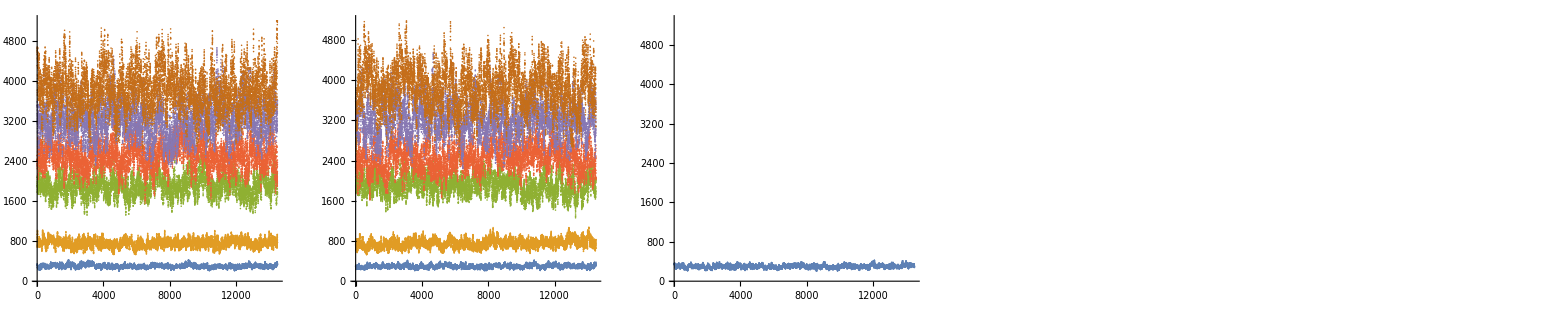

```mathematica
GraphicsGrid[{Table[ListPlot[Table[Transpose[dudldatavol[[j]][[i]]][[3]],{i,1,6}]],{j,1,5}]},ImageSize->4000]
```

```mathematica
Table[Mean@Transpose[dudldatavol[[1]][[i]]][[3]],{i,1,6}]
Table[StandardDeviation@Transpose[dudldatavol[[1]][[i]]][[3]],{i,1,6}]
```

{300.741,761.27,1914.55,2523.57,3227.33,3813.34}

{31.0065,73.7148,205.219,263.824,331.255,383.364}

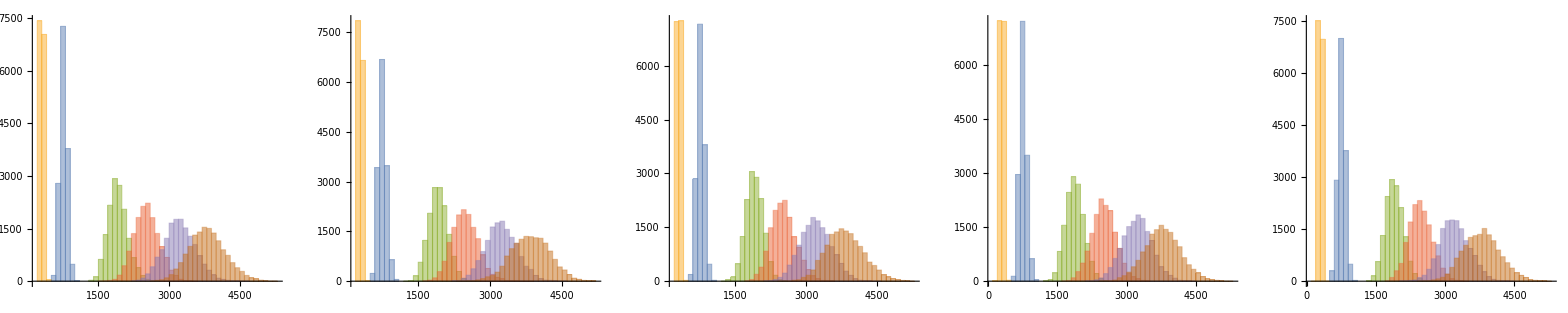

```mathematica
GraphicsGrid[{Table[Show@Histogram[Table[Transpose[dudldatavol[[j]][[i]]][[3]],{i,1,6}],50],{j,1,5}]},ImageSize->2000]
```

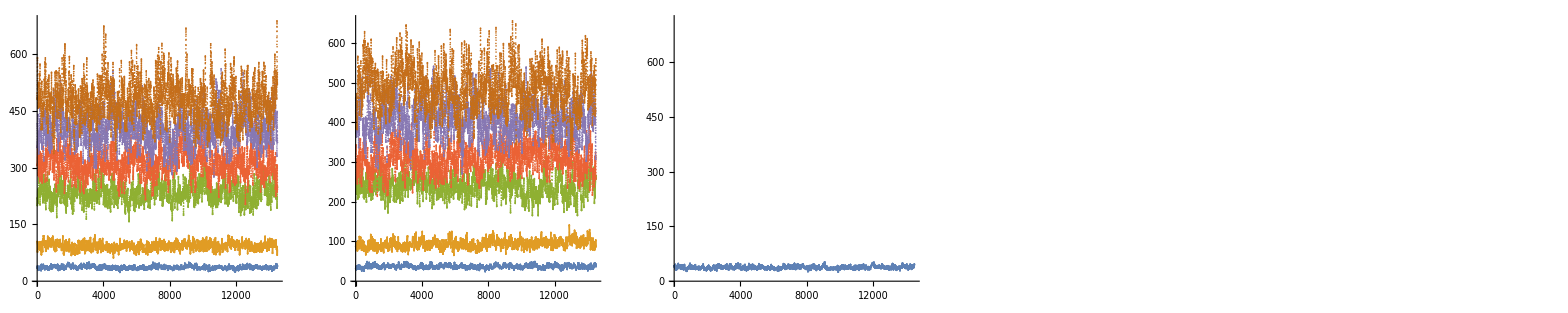

```mathematica
(*U (meV/at) col 5*)
GraphicsGrid[{Table[ListPlot[Table[Transpose[dudldatavol[[j]][[i]]][[5]],{i,1,6}]],{j,1,5}]},ImageSize->4000]
```

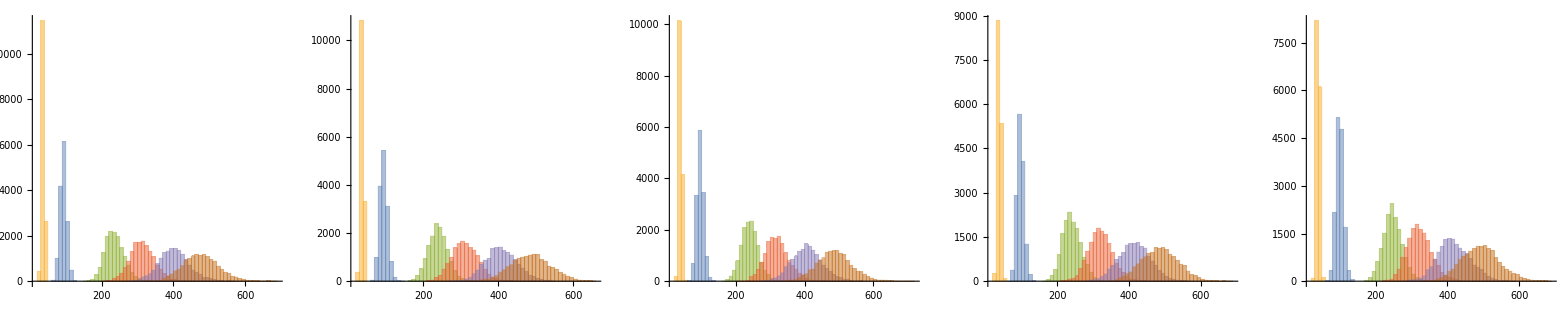

```mathematica
GraphicsGrid[{Table[Show@Histogram[Table[Transpose[dudldatavol[[j]][[i]]][[5]],{i,1,6}],50],{j,1,5}]},ImageSize->2000]
```

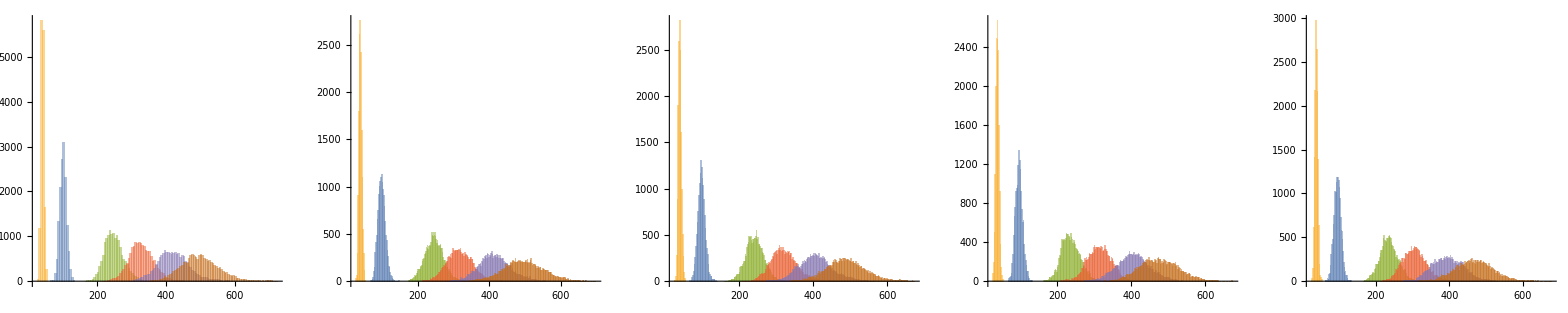

```mathematica
(*Ureference*)
GraphicsGrid[{Table[Show@Histogram[Table[Transpose[dudldatavol[[j]][[i]]][[6]],{i,1,6}],200],{j,1,5}]},ImageSize->2000]
```

```mathematica
plot[thing_,max_]:=GraphicsGrid[{Table[Show[ListPlot[Table[Table[thing[[j]][[i]][[l]],{i,1,5}],{j,1,6}]],ListPlot[Table[Table[thing[[j]][[i]][[l]],{i,1,5}],{j,1,6}],Joined->True]],{l,1,max}]},ImageSize->1200]
```

```mathematica
skewnormalTemp=Table[Table[EstimatedDistribution[Transpose[dudldatavol[[i]][[j]]][[4]],SkewNormalDistribution[μ,σ,α]],{i,1,5}],{j,1,6}]
```

{{SkewNormalDistribution[300.297,4.21644,1.46681],SkewNormalDistribution[293.522,6.58909,-0.3988],SkewNormalDistribution[297.654,2.17549,3.13142],SkewNormalDistribution[293.212,6.26151,-1.41125×10^-7],SkewNormalDistribution[293.674,3.2356,-0.0274189]},{SkewNormalDistribution[749.623,14.3133,-0.185081],SkewNormalDistribution[756.478,23.6293,-597.632],SkewNormalDistribution[740.54,20.5137,-1.94354×10^-6],SkewNormalDistribution[738.8,26.3165,17917.5],SkewNormalDistribution[744.207,12.1211,-2.4715×10^-6]},{SkewNormalDistribution[1881.82,26.1079,3.69191×10^-8],SkewNormalDistribution[1905.99,39.1815,-0.266017],SkewNormalDistribution[1869.25,35.712,-7.65547×10^-7],SkewNormalDistribution[1839.72,47.147,9.10744×10^-8],SkewNormalDistribution[1906.71,21.5165,-1.68347]},{SkewNormalDistribution[2492.64,40.6758,-1.84695×10^-8],SkewNormalDistribution[2471.03,82.1151,-5.06371],SkewNormalDistribution[2466.14,54.4722,1.98923×10^-7],SkewNormalDistribution[2418.75,102.091,-3.66032×10^-7],SkewNormalDistribution[2442.21,53.2714,-0.290696]},{SkewNormalDistribution[3167.33,76.109,-0.18413],SkewNormalDistribution[3225.23,31.52,-0.307903],SkewNormalDistribution[3173.42,38.2797,-1.29699×10^-7],SkewNormalDistribution[3211.27,66.871,-3.13169],SkewNormalDistribution[3176.45,52.9837,-0.267899]},{SkewNormalDistribution[3793.37,42.2312,-0.0790399],SkewNormalDistribution[3822.9,72.256,-0.117784],SkewNormalDistribution[3815.84,72.1373,-171.883],SkewNormalDistribution[3766.78,27.4074,-0.130417],SkewNormalDistribution[3785.79,65.5454,-0.144039]}}

```mathematica
normalTemp=Table[Table[EstimatedDistribution[Transpose[dudldatavol[[i]][[j]]][[4]],NormalDistribution[μ,σ]],{i,1,5}],{j,1,6}]
```

{{NormalDistribution[303.064,3.18208],NormalDistribution[291.897,6.45318],NormalDistribution[299.2,1.53014],NormalDistribution[293.212,6.26151],NormalDistribution[293.604,3.23586]},{NormalDistribution[747.867,14.3085],NormalDistribution[736.097,11.955],NormalDistribution[740.54,20.5137],NormalDistribution[764.746,4.39784],NormalDistribution[744.207,12.1211]},{NormalDistribution[1881.82,26.1079],NormalDistribution[1899.13,38.8389],NormalDistribution[1869.25,35.712],NormalDistribution[1839.72,47.147],NormalDistribution[1892.57,16.2162]},{NormalDistribution[2492.64,40.6758],NormalDistribution[2412.43,57.8553],NormalDistribution[2466.14,54.4722],NormalDistribution[2418.75,102.091],NormalDistribution[2432.29,52.759]},{NormalDistribution[3157.45,75.7322],NormalDistribution[3218.9,31.1175],NormalDistribution[3173.42,38.2797],NormalDistribution[3164.8,48.815],NormalDistribution[3167.34,52.6332]},{NormalDistribution[3790.84,42.2016],NormalDistribution[3816.74,72.1746],NormalDistribution[3763.24,49.3706],NormalDistribution[3764.12,27.3407],NormalDistribution[3778.91,65.3394]}}

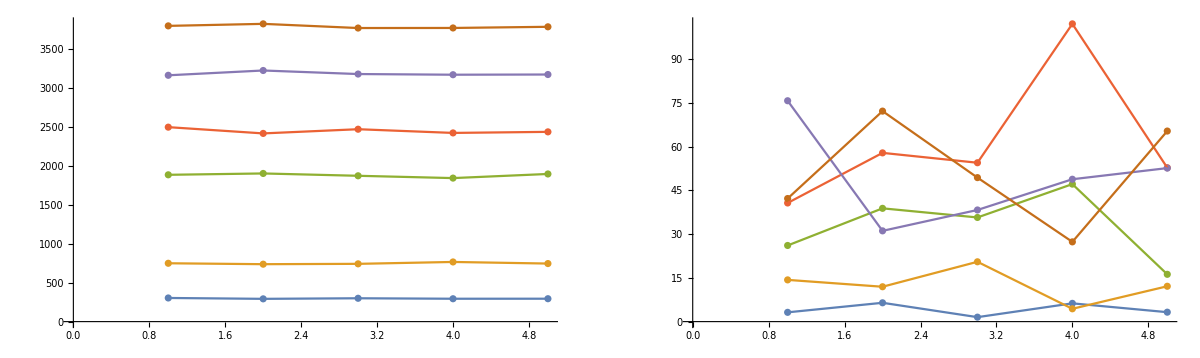

```mathematica
plot[normalTemp,2]
```

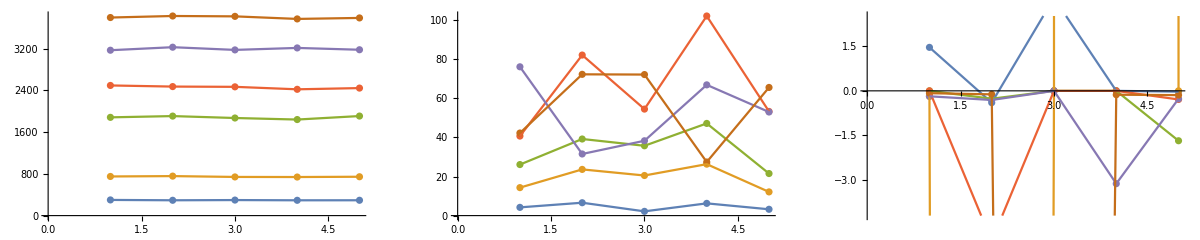

```mathematica
plot[skewnormalTemp]
```

```mathematica
skewnormalTemp//TableForm
```

SkewNormalDistribution[300.297,4.21644,1.46681] | SkewNormalDistribution[293.522,6.58909,-0.3988] | SkewNormalDistribution[297.654,2.17549,3.13142] | SkewNormalDistribution[293.212,6.26151,-1.41125×10^-7] | SkewNormalDistribution[293.674,3.2356,-0.0274189]
SkewNormalDistribution[749.623,14.3133,-0.185081] | SkewNormalDistribution[756.478,23.6293,-597.632] | SkewNormalDistribution[740.54,20.5137,-1.94354×10^-6] | SkewNormalDistribution[738.8,26.3165,17917.5] | SkewNormalDistribution[744.207,12.1211,-2.4715×10^-6]
SkewNormalDistribution[1881.82,26.1079,3.69191×10^-8] | SkewNormalDistribution[1905.99,39.1815,-0.266017] | SkewNormalDistribution[1869.25,35.712,-7.65547×10^-7] | SkewNormalDistribution[1839.72,47.147,9.10744×10^-8] | SkewNormalDistribution[1906.71,21.5165,-1.68347]
SkewNormalDistribution[2492.64,40.6758,-1.84695×10^-8] | SkewNormalDistribution[2471.03,82.1151,-5.06371] | SkewNormalDistribution[2466.14,54.4722,1.98923×10^-7] | SkewNormalDistribution[2418.75,102.091,-3.66032×10^-7] | SkewNormalDistribution[2442.21,53.2714,-0.290696]
SkewNormalDistribution[3167.33,76.109,-0.18413] | SkewNormalDistribution[3225.23,31.52,-0.307903] | SkewNormalDistribution[3173.42,38.2797,-1.29699×10^-7] | SkewNormalDistribution[3211.27,66.871,-3.13169] | SkewNormalDistribution[3176.45,52.9837,-0.267899]
SkewNormalDistribution[3793.37,42.2312,-0.0790399] | SkewNormalDistribution[3822.9,72.256,-0.117784] | SkewNormalDistribution[3815.84,72.1373,-171.883] | SkewNormalDistribution[3766.78,27.4074,-0.130417] | SkewNormalDistribution[3785.79,65.5454,-0.144039]

```mathematica
skewnormalU=Table[Table[EstimatedDistribution[Transpose[dudldatavol[[i]][[j]]][[5]],SkewNormalDistribution[μ,σ,α]],{i,1,5}],{j,1,6}];
normalU=Table[Table[EstimatedDistribution[Transpose[dudldatavol[[i]][[j]]][[5]],NormalDistribution[μ,σ]],{i,1,5}],{j,1,6}];
```

$Aborted

```mathematica
skewnormalUref=Table[Table[EstimatedDistribution[Transpose[dudldatavol[[i]][[j]]][[6]],SkewNormalDistribution[μ,σ,α]],{i,1,5}],{j,1,6}]
```

{{SkewNormalDistribution[36.7444,5.5359,1.52356],SkewNormalDistribution[35.6025,5.61426,1.5439],SkewNormalDistribution[35.5198,5.56696,1.63117],SkewNormalDistribution[36.502,4.72993,0.710747],SkewNormalDistribution[35.2204,4.85007,1.09413]},{SkewNormalDistribution[95.1485,11.0225,0.790233],SkewNormalDistribution[89.7261,13.8352,1.47951],SkewNormalDistribution[90.4883,12.3765,1.20384],SkewNormalDistribution[89.4634,12.2381,1.27773],SkewNormalDistribution[89.9044,11.3661,0.868897]},{SkewNormalDistribution[222.786,37.0645,1.79754],SkewNormalDistribution[228.468,30.3648,0.984214],SkewNormalDistribution[224.552,30.2623,1.12475],SkewNormalDistribution[215.216,32.3985,1.44056],SkewNormalDistribution[215.95,31.5723,1.32598]},{SkewNormalDistribution[303.909,41.4626,1.05703],SkewNormalDistribution[290.857,43.5583,1.1511],SkewNormalDistribution[289.387,46.335,1.60393],SkewNormalDistribution[293.579,38.7743,0.938607],SkewNormalDistribution[279.399,40.391,1.32606]},{SkewNormalDistribution[383.719,57.6201,1.38033],SkewNormalDistribution[380.851,54.6549,1.26972],SkewNormalDistribution[371.31,56.6213,1.29411],SkewNormalDistribution[382.709,48.4328,0.730544],SkewNormalDistribution[365.756,51.4397,1.12037]},{SkewNormalDistribution[451.716,71.3604,1.57451],SkewNormalDistribution[460.596,64.8249,0.940674],SkewNormalDistribution[449.858,64.0051,1.15406],SkewNormalDistribution[437.603,63.1322,1.12981],SkewNormalDistribution[436.278,59.2059,0.943127]}}

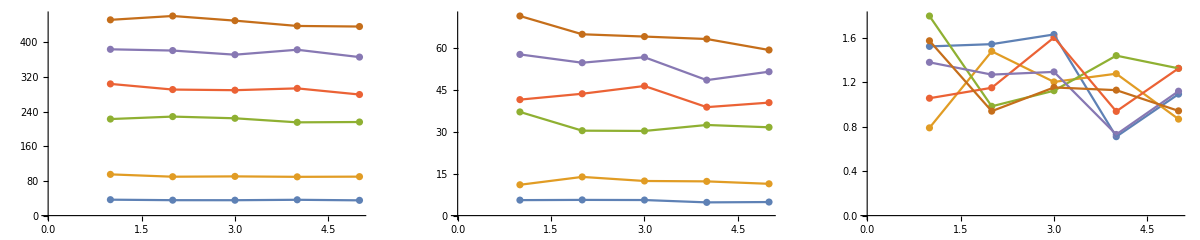

```mathematica
plot[skewnormalUref]
```

```mathematica
skewnormaldUdL=Table[Table[EstimatedDistribution[Transpose[dudldatavol[[i]][[j]]][[7]],SkewNormalDistribution[μ,σ,α]],{i,1,5}],{j,1,6}]
```

{{SkewNormalDistribution[-3.28616,0.7549,-1.66997],SkewNormalDistribution[-1.90082,0.602614,-1.30248],SkewNormalDistribution[-1.01737,0.574983,-1.10611],SkewNormalDistribution[-0.305392,0.583465,0.929935],SkewNormalDistribution[0.980654,0.65287,0.670525]},{SkewNormalDistribution[-6.94784,1.60869,-0.48832],SkewNormalDistribution[-5.64798,1.94315,1.33268],SkewNormalDistribution[-3.74119,2.032,1.48862],SkewNormalDistribution[-1.10444,2.29428,1.51253],SkewNormalDistribution[1.74508,2.8414,1.49463]},{SkewNormalDistribution[-16.1479,6.56676,0.797007],SkewNormalDistribution[-9.99758,7.20896,0.935486],SkewNormalDistribution[-6.61764,7.88334,1.08599],SkewNormalDistribution[-2.30381,9.25504,1.61056],SkewNormalDistribution[3.40134,11.7921,1.80061]},{SkewNormalDistribution[-20.4885,10.6087,0.891022],SkewNormalDistribution[-13.3959,12.0434,1.32692],SkewNormalDistribution[-7.93966,12.3879,0.972558],SkewNormalDistribution[-2.24894,13.7174,1.21385],SkewNormalDistribution[4.03306,17.6762,1.89927]},{SkewNormalDistribution[-26.4947,15.4038,0.778913],SkewNormalDistribution[-15.1868,16.0051,0.827205],SkewNormalDistribution[-10.2935,17.8179,0.987171],SkewNormalDistribution[-4.23323,21.321,1.4062],SkewNormalDistribution[5.36673,23.7765,1.63978]},{SkewNormalDistribution[-33.7897,19.6604,0.968371],SkewNormalDistribution[-2.91651,19.6752,-0.519332],SkewNormalDistribution[-15.4619,23.6042,1.14064],SkewNormalDistribution[-7.48969,26.8618,1.50269],SkewNormalDistribution[6.41506,28.1705,1.2298]}}

```mathematica
normaldUdL=Table[Table[EstimatedDistribution[Transpose[dudldatavol[[i]][[j]]][[7]],NormalDistribution[μ,σ]],{i,1,5}],{j,1,6}]
```

{{NormalDistribution[-3.80361,0.549657],NormalDistribution[-2.28181,0.466892],NormalDistribution[-1.35737,0.463691],NormalDistribution[0.0115234,0.489894],NormalDistribution[1.27071,0.5849]},{NormalDistribution[-7.51105,1.50688],NormalDistribution[-4.40953,1.49735],NormalDistribution[-2.39832,1.52503],NormalDistribution[0.419854,1.71471],NormalDistribution[3.61836,2.13644]},{NormalDistribution[-12.8838,5.69806],NormalDistribution[-6.07116,6.04586],NormalDistribution[-1.99575,6.38632],NormalDistribution[3.95867,6.81448],NormalDistribution[11.5971,8.47836]},{NormalDistribution[-14.8638,8.99484],NormalDistribution[-5.72886,9.28761],NormalDistribution[-1.05372,10.2977],NormalDistribution[6.1837,10.8193],NormalDistribution[16.5258,12.5053]},{NormalDistribution[-18.9447,13.4267],NormalDistribution[-7.05125,13.7832],NormalDistribution[-0.30572,14.7554],NormalDistribution[9.60593,16.2193],NormalDistribution[21.5628,17.4072]},{NormalDistribution[-22.8879,16.361],NormalDistribution[-10.1511,18.2968],NormalDistribution[-1.30944,18.8908],NormalDistribution[10.354,20.0788],NormalDistribution[23.8352,22.1386]}}

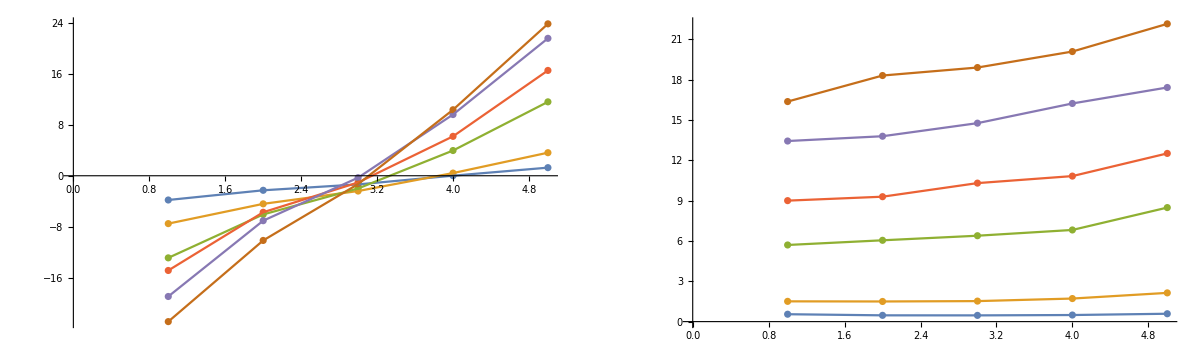

```mathematica
plot[normaldUdL,2]
```

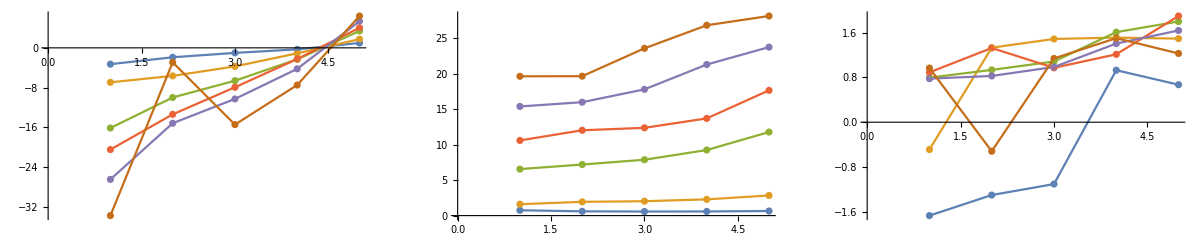

```mathematica
plot[skewnormaldUdL]
```

```mathematica
skewnormalAvergagedUdL=Table[Table[EstimatedDistribution[Transpose[dudldatavol[[i]][[j]]][[8]],SkewNormalDistribution[μ,σ,α]],{i,1,5}],{j,1,6}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{{SkewNormalDistribution[-3.81713,0.0616289,-3.08313],SkewNormalDistribution[-2.26658,0.0513693,6.9338],SkewNormalDistribution[-1.37487,0.0440735,-0.332224],SkewNormalDistribution[0.0707545,0.0568041,-1.94154],SkewNormalDistribution[1.23313,0.0278035,1.77872]},{SkewNormalDistribution[-7.41389,0.169614,0.25112],SkewNormalDistribution[-4.3819,0.0755675,2.84528],SkewNormalDistribution[-2.44066,0.0845664,4.40738],SkewNormalDistribution[0.505582,0.07697,-1.55617],SkewNormalDistribution[3.70307,0.16152,-1.9003]},{SkewNormalDistribution[-12.6373,0.241706,-3.52639],SkewNormalDistribution[-6.03136,0.307636,7.97703×10^-8],SkewNormalDistribution[-1.94197,0.331816,-3.47212],SkewNormalDistribution[3.92096,0.343418,-0.135883],SkewNormalDistribution[11.223,0.48062,1.48508]},{SkewNormalDistribution[-14.951,0.682265,24.9924],SkewNormalDistribution[-5.25217,0.481483,-18.0069],SkewNormalDistribution[-0.856333,0.43245,-3.2738],SkewNormalDistribution[7.11251,0.907454,-2.8628],SkewNormalDistribution[16.2994,0.463568,2.94405×10^-8]},{SkewNormalDistribution[-18.23,0.602777,3.33635×10^-8],SkewNormalDistribution[-7.68605,1.02663,6.67527],SkewNormalDistribution[0.207432,0.610038,-2.18627],SkewNormalDistribution[9.66979,1.45972,1.9327],SkewNormalDistribution[20.9319,0.773792,-3.29278×10^-6]},{SkewNormalDistribution[-22.5395,0.82133,1.89107×10^-7],SkewNormalDistribution[-10.5269,0.562758,0.941871],SkewNormalDistribution[-1.34885,0.662784,-2.52355],SkewNormalDistribution[11.3424,0.982368,-1.47014],SkewNormalDistribution[23.6992,1.47564,-0.360755]}}

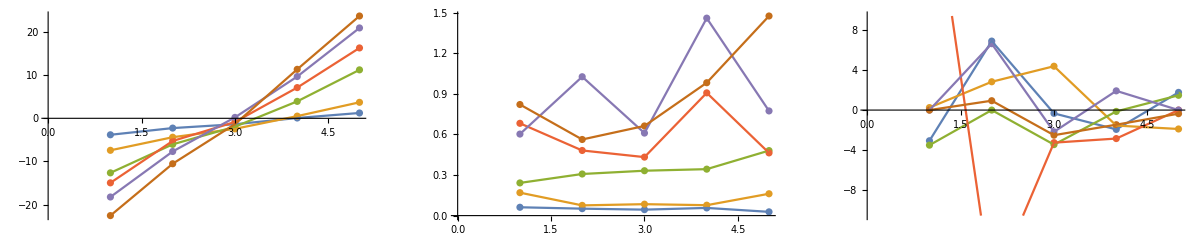

```mathematica
plot[skewnormalAvergagedUdL]
```

```mathematica
plot[skewnormalAvergagedUdL]
```

-Graphics-

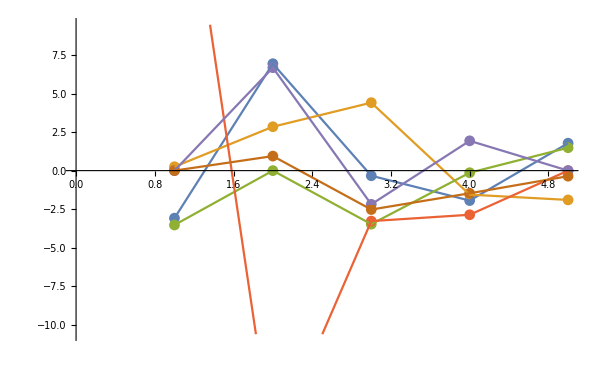

```mathematica
Show[ListPlot[Table[Table[skewnormalAvergagedUdL[[j]][[i]][[3]],{i,1,5}],{j,1,6}]],ListPlot[Table[Table[skewnormalAvergagedUdL[[j]][[i]][[3]],{i,1,5}],{j,1,6}],Joined->True]]
```

```mathematica
(*step time(fs) temp(K) average U(meV/at) Uref dUdL average offset*)
```

```mathematica
(*dUdL (meV/at) col 7*)
```

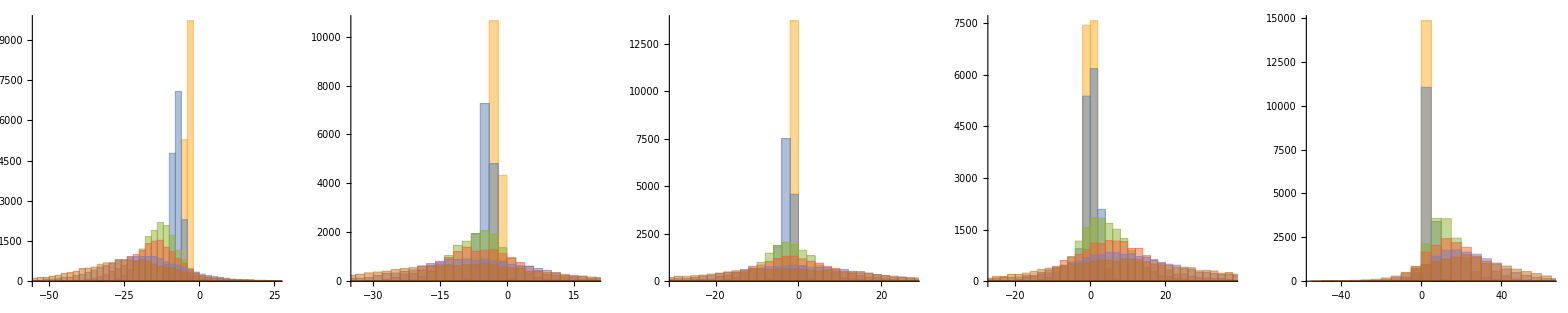

```mathematica
GraphicsGrid[{Table[Show@Histogram[Table[Transpose[dudldatavol[[j]][[i]]][[7]],{i,1,6}],50],{j,1,5}]},ImageSize->2000]
```

```mathematica
GraphicsGrid[{Table[Show@Histogram[Table[Transpose[dudldatavol[[j]][[i]]][[7]],{i,1,6}],50],{j,1,5}]},ImageSize->2000]
```

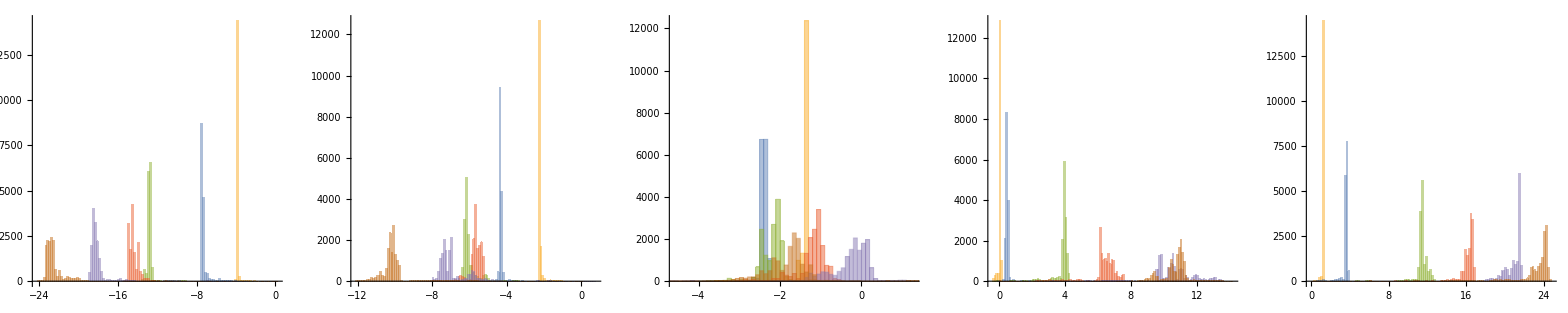

```mathematica
GraphicsGrid[{Table[Show@Histogram[Table[Transpose[dudldatavol[[j]][[i]]][[8]],{i,1,6}],100],{j,1,5}]},ImageSize->2000]
```